# Point Force Greens Functions (force)

```mathematica
Get["/Users/mallickrishg/Downloads/mathematica2matlab/mathematica2matlab/ToMatlab.m"]
r = Sqrt[(x-xs)^2 +(y-ys)^2];
Upt =1/2/Pi*Log[r]
(*ex = D[Upt,x]
ey = D[Upt,y]*)
```

Log[√((x-xs)^2+(y-ys)^2)]/(2 π)

## Integration over a constant source defined from y in [-W,W]

```mathematica
Uconst1d = Integrate[ReplaceAll[Upt,{ys->0}],{xs,-w,w},GenerateConditions->False]
(*Uconst1d =ReplaceAll[Uconst,{ys->w,xs->0}]-ReplaceAll[Uconst,{ys->-w,xs->0}]//FullSimplify*)
```

(-4 w+2 y (ArcTan[(w-x)/y]+ArcTan[(w+x)/y])+(w-x) Log[(w-x)^2+y^2]+(w+x) Log[(w+x)^2+y^2])/(4 π)

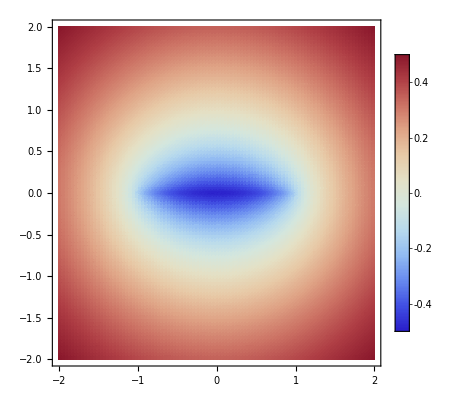

```mathematica
DensityPlot[ReplaceAll[Uconst1d,{w->1}],{x,-2,2},{y,-2,2},ColorFunction->"ThermometerColors",PlotLegends->BarLegend[{Automatic,{-0.5,0.5}}],PlotPoints->100,PlotRange->{-0.5,0.5}]
```

## Integrate point source with linear force function over the domain y in [-W,W]

```mathematica
ULinB1 = Integrate[Upt*(1+1/w*xs),xs,GeneratedParameters->C];
ULinB2 = Integrate[Upt*(1-1/w*xs),xs,GeneratedParameters->C];
ULin1dB1 =ReplaceAll[ULinB1,{xs->w,ys->0}]-ReplaceAll[ULinB1,{xs->-w,ys->0}]//FullSimplify
ULin1dB2 =ReplaceAll[ULinB2,{xs->w,ys->0}]-ReplaceAll[ULinB2,{xs->-w,ys->0}]//FullSimplify
ToMatlab[ULin1dB1]
ToMatlab[ULin1dB2]
```

1/(8 π w)(-4 w (2 w+x)+4 (w+x) y ArcTan[(w-x)/y]+4 (w+x) y ArcTan[(w+x)/y]+((w-x) (3 w+x)+y^2) Log[(w-x)^2+y^2]+(w+x-y) (w+x+y) Log[(w+x)^2+y^2])

1/(8 π w)(4 w (-2 w+x)+4 (w-x) y ArcTan[(w-x)/y]+4 (w-x) y ArcTan[(w+x)/y]+(w-x-y) (w-x+y) Log[(w-x)^2+y^2]+((3 w-x) (w+x)+y^2) Log[(w+x)^2+y^2])

(1/8).*pi.^(-1).*w.^(-1).*((-4).*w.*(2.*w+x)+4.*(w+x).*y.*atan((w+ ...
  (-1).*x).*y.^(-1))+4.*(w+x).*y.*atan((w+x).*y.^(-1))+((w+(-1).*x) ...
  .*(3.*w+x)+y.^2).*log((w+(-1).*x).^2+y.^2)+(w+x+(-1).*y).*(w+x+y) ...
  .*log((w+x).^2+y.^2));

(1/8).*pi.^(-1).*w.^(-1).*(4.*w.*((-2).*w+x)+4.*(w+(-1).*x).*y.* ...
  atan((w+(-1).*x).*y.^(-1))+4.*(w+(-1).*x).*y.*atan((w+x).*y.^(-1)) ...
  +(w+(-1).*x+(-1).*y).*(w+(-1).*x+y).*log((w+(-1).*x).^2+y.^2)+(( ...
  3.*w+(-1).*x).*(w+x)+y.^2).*log((w+x).^2+y.^2));

```mathematica
DensityPlot[{ReplaceAll[ULin1dB1,{w->1}],ReplaceAll[ULin1dB2,{w->1}]},{x,-2,2},{y,-2,2},ColorFunction->"ThermometerColors",PlotLegends->Automatic,PlotRange->{-1,1},PlotPoints->100,PlotRange->{-0.5,0.5}]
```

-Graphics-

```mathematica
exB1 = D[ULin1dB1,x]//FullSimplify
exB2 = D[ULin1dB2,x]//FullSimplify
eyB1 = D[ULin1dB1,y]//FullSimplify
eyB2 = D[ULin1dB2,y]//FullSimplify
```

-(-4 w+2 y (ArcTan[(w-x)/y]+ArcTan[(w+x)/y])+(w-x) (Log[(w-x)^2+y^2]-Log[(w+x)^2+y^2]))/(4 π w)

(2 (w-x) (ArcTan[(w-x)/y]+ArcTan[(w+x)/y])+y (-Log[(w-x)^2+y^2]+Log[(w+x)^2+y^2]))/(4 π w)

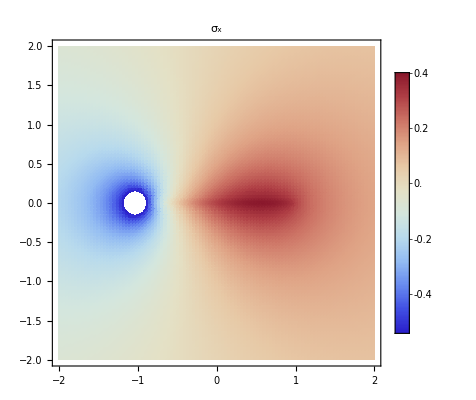

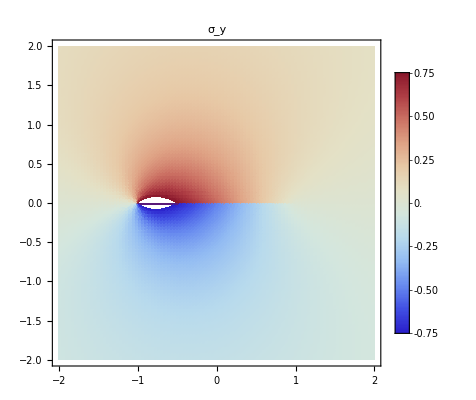

```mathematica
DensityPlot[ReplaceAll[ex,{w->1,a0->1,a1->1}],{x,-2,2},{y,-2,2},ColorFunction->"ThermometerColors",PlotLegends->Automatic,PlotPoints->100,PlotLabel->Subscript[σ, x]]
DensityPlot[ReplaceAll[ey,{w->1,a0->1,a1->1}],{x,-2,2},{y,-2,2},ColorFunction->"ThermometerColors",PlotLegends->Automatic,PlotPoints->100,PlotRange->{-0.75,0.75},PlotLabel->Subscript[σ, y]]
```

## Plot a cross section of displacements and stresses at x = 0

```mathematica
yeval=0.000001;
weval = 1;
a0eval = 1;
a1eval = 1;
Plot[ReplaceAll[Ulin1d,{w->weval,y->yeval}],{x,-2,2},PlotLabels->"displacement",Filling->Axis,AxesLabel->{x,u[x]},PlotStyle->{Thick,Black}]
Plot[{ReplaceAll[ex,{w->weval,y->yeval}],ReplaceAll[ey,{w->weval,a0->a0eval,a1->a1eval,y->yeval}]},{x,-2,2},AxesLabel->{x,Stress},PlotLabels->{Subscript[σ, x],Subscript[σ, y]}]
```

-Graphics-

-Graphics-